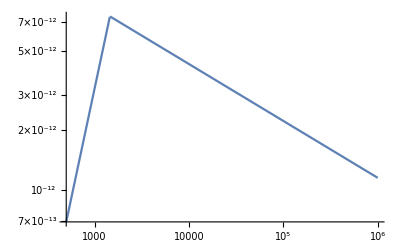

```mathematica
Norma=7.44162 10^(-12);
Eb=1451.78 MeV;
α=2.22699;
β=0.285398;
dNdE[E_]:=Norma  Piecewise[{{(E/Eb)^α,E<Eb},{(E/Eb)^-β,E>Eb}}];
MeV=1;
LogLogPlot[dNdE[x],{x,5 10^2 MeV, 10^6 MeV}]
```

5.668×10^-8

| Estimate | Standard Error | t-Statistic | P-Value
L0 | 563.01 | 600.818 | 0.937073 | 0.363565
σ | 0.722374 | 0.812936 | 0.888599 | 0.388247

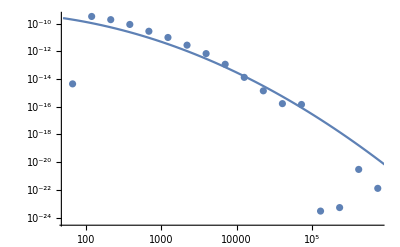

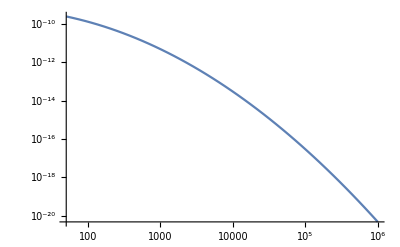

```mathematica
Clear[L0,σ];
POINTS={{66.9067600897004,4.47195848319138*10^-15},{119.803636291152,3.28573703618838*10^-10},{214.523562257219,1.93149352607856*10^-10},{384.131568858944,8.71242225064711*10^-11},{687.828235918586,2.81146443945828*10^-11},{1231.62926580659,9.99637281262781*10^-12},{2205.36257335447,2.78627997751418*10^-12},{3948.93513411886,6.83891975056633*10^-13},{7071.06777656652,1.16170176182305*10^-13},{12661.6411266918,1.31963913080858*10^-14},{22672.0087231483,1.40733883202488*10^-15},{40596.6315424086,1.67620063742623*10^-16},{72692.5660939508,1.45835586714352*10^-16},{130163.734392676,2.94446755533894*10^-24},{233074.628141995,5.27209288655176*10^-24},{417349.598465317,2.99686879354038*10^-21},{747308.634191276,1.28807303405685*10^-22}};
Norma=NIntegrate[Interpolation[POINTS][x],{x,67,747}]
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);
F1=NonlinearModelFit[POINTS,Norma  F[x],{{L0,9.00145 10},{σ,7.42744 10^-1}},x];
F1["ParameterTable"]

(*ROOT FIT VALUES*)
L0=9.00145 10; (*This is an energy, not a luminosity*)
σ=7.42744 10^-1;

Show[ListLogLogPlot[POINTS],LogLogPlot[Norma   F[x],{x,5 10, 10^6}]]
LogLogPlot[Norma F[x],{x,5 10, 10^6}]
```

```mathematica
(*LUMINOSITY OF TERZAN 5*)
Clear[MeV,erg,cm,kpc,s];
MeV=1.60218 10^(-6) erg;
TotalEnergyPerTimeArea=NIntegrate[Interpolation[POINTS][x]*x,{x,67,747}] MeV/(cm^2 s)
TotalEnergyPerTimeArea=Norma NIntegrate[F[x]*x,{x,0,Infinity}] MeV/(cm^2 s)
TimeofPointing=(620181124-239557417 )s;
R=5.98 kpc;
kpc=3.086 10^21 cm;
cm=1;
Luminosity=4 Pi R^2 TotalEnergyPerTimeArea (*erg/s*)
LO=3.846 10^(33) erg/s;
(*erg=1;
s=1;*)
Luminosity/LO
(*This luminosity includes only the gamma part*)
```

(2.43392×10^-11 erg)/(cm^2 s)

(3.52846×10^-11 erg)/(cm^2 s)

(1.51004×10^35 erg)/s

39.2627

{{NGCE→1100.56}}

{0.}

{0.}

6.32849×10^40

```mathematica
(*Here we should find dN/dL*)
```

```mathematica
(*FIND NGCE [COMPLETE MODEL]*)
(*DISK has different limits of integration 1e30 and 1e37*)
Clear[kpc,cm,R0,rc,ρ,rLat,FGCE,NGCE,A,Nr,Normalization,sol,Func];
FGCE=1.8 10^-9;
R0=8.5 kpc; (*If we assume all MSPs are in the galactic center*)
rc=20 kpc;
kpc=3.086 10^21 cm;
cm=1;
ρ[r_]:=(r/rc)^(-2γ)  (1+r/rc)^(-6+2 γ);
γ=1.2;
rLat[s_,b_,l_]:=Sqrt[R0^2+s^2-2 R0 s Cos[b] Cos[l]];
Lmin=10^30;
Lmax=10^37;
wp=50;
Normalization=NIntegrate[F[L],{L,Lmin,Lmax},WorkingPrecision->wp,PrecisionGoal->10,MinRecursion->9];
Func[L_]:=F[L]/Normalization;
L0=4.3 10^32;
Lth=10^34;

(*,Method->"GlobalAdaptive",MinRecursion->6; Method->"Trapezoidal"*)
sol=NSolve[A NIntegrate[x Func[x] ,{x,Lmin,Lmax},MinRecursion->9,WorkingPrecision->wp,PrecisionGoal->10]  NIntegrate[ ρ[rLat[s,b,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree},Method->"GlobalAdaptive"]/(4 Pi)-FGCE==0,A]  
NGCE= NIntegrate[s^2 ρ[rLat[s,b,l]] Cos[b] UnitStep[Abs[b]-2 Degree],{s,0,Infinity},{b,-20 Degree,20 Degree},{l,0,20 Degree}] A/.sol
(*Nr=NIntegrate[Func[x]  s^2 ρ[rLat[s,b,l]] Sin[b],{x,4 Pi s^2 Fth,Lmax}, {s,0,Infinity},{b,2 Degree,20 Degree},{l,-20  Degree,20 Degree},Method->"GlobalAdaptive",MinRecursion->8] A/.sol*)


Clear[NGCE];
sol=NSolve[NGCE NIntegrate[x Func[x],{x,Lmin,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30]== FGCE/(1.11 10^-46),NGCE]
Nr=NGCE NIntegrate[Func[x],{x,Lth,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30] /.sol
Rr=NGCE NIntegrate[x Func[x],{x,Lth,Lmax},MinRecursion->9,WorkingPrecision->wp,AccuracyGoal->Infinity,PrecisionGoal->30]/(FGCE/(1.11 10^-46)) /.sol
```

InterpolatingFunction[…]

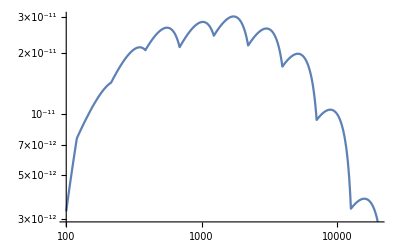

```mathematica
(*Plot in erg*)
Clear[MeV,erg];
Function1=Interpolation[POINTS,InterpolationOrder->1]
MeV=1.60218 10^(-6) erg;
erg=1;
LogLogPlot[x^2 Function1[x] MeV,{x,10^2,2 10^4}]
```

```mathematica
(*LOOK AT PARAMETER SPACE*)
Clear[L0,σ];
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);
Luminosity=(1.5100439594284642*^35 erg)/s;
erg=1;
s=1;
sol=Solve[Luminosity==Integrate[x F[x],{x,0,Infinity}],{L0,σ}]
LogLogPlot[L0/.sol,{σ,0,100}]
```

{{L0→ConditionalExpression[(1.51004×10^35 2.71828^(-2.65095 σ^2))/(√(1/σ^2) σ),(-1. Re[σ]<Im[σ]<Re[σ]&&Re[σ]>0)||(Re[σ]<Im[σ]<-1. Re[σ]&&Re[σ]<0)]}}

-Graphics-

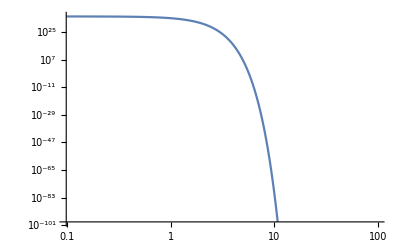

```mathematica
LogLogPlot[L0/.sol,{σ,0,100}]
```